```mathematica
(*Line Charge Distributin*)
(*Load necessary packages*)
<<VectorAnalysis`(*for command of vector analysis*)
<<VectorFieldPlots` (*for drawing field patterns*)
```

```mathematica
(*Define a function which can be used to find electric potential of a single electric charge*)
pot[{Q_,x0_,y0_,z0_}]:=Q/(4π ϵ Sqrt[(x-x0)^2+(y-y0)^2+(z-z0)^2])
(*here x0,y0, z0 are the coordinates of the position of electric charge and x,y,z are the coordinates of any point where electric potential or electric field intensity can be found*)
```

```mathematica
(*no. of charges*)n=10;xmin=-5;xmax=5;delx=(xmax-xmin)/(n-1);
(*generate the distribution*)
LineDist=Table[{0.001,xmin+(i-1)*delx,0,0},{i,1,10}];
LinePot=Sum[pot[LineDist[[i]]],{i,1,10}]
LinePotxy=LinePot/.{ϵ->1,z->0}
Plot3D[LinePotxy,{x,-6,6},{y,-2,2},PlotRange->{{-6,6},{-2,2},{0,0.003}},PlotPoints->200]
ContourPlot[LinePotxy,{x,-6,6},{y,-2,2},PlotRange->{{-6,6},{-2,2}},Contours->20,PlotPoints->50]
```

```mathematica
(*Compute Electric Field Intensity*)
ELineInt=-Grad[LinePot,Cartesian[x,y,z]]
MagExy=Norm[ELineInt]/.{ϵ->1,z->0}
Plot3D[MagExy,{x,-6,6},{y,-2,2},PlotRange->{{-6,6},{-2,2},{0,0.0025}},PlotPoints->100]
(*Plot the components of electric field intensity*)
Plot3D[ELineInt/.{ϵ->1,z->0},{x,-6,6},{y,-2,2},PlotRange->{{-6,6},{-2,2},{-0.0025,0.0025}},PlotPoints->100]
```

-Graphics3D-

-Graphics3D-

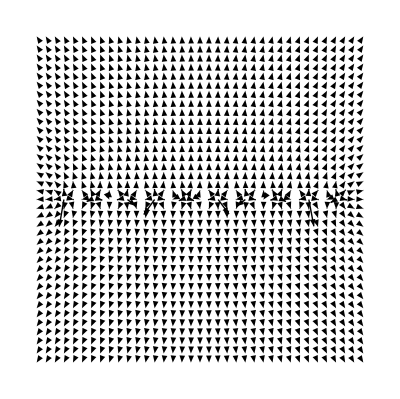

-Graphics3D-

```mathematica
VectorFieldPlot[{ELineInt[[1]],ELineInt[[2]]}/.{ϵ->1,z->0},{x,-6,6,0.33},{y,-6,6,0.33},ScaleFactor->1,MaxArrowLength->2]
VectorFieldPlot3D[ELineInt/.ϵ->1,{x,-6,6,0.31},{y,-2,2,0.31},{z,-2,2,0.31},ScaleFactor->1,MaxArrowLength->2,VectorHeads->True]
```